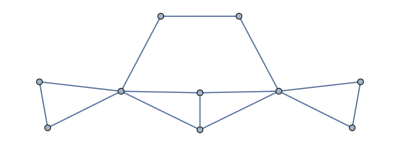

```mathematica
graph = Import["/Users/josephhenderson/Desktop/Research/EquitablePartitions/Mathematica/exported_graph.graphml"]
```

```mathematica
A = Normal[AdjacencyMatrix[graph]]
```

{{0,0,1,0,1,0,1,0,1,1},{0,0,0,1,0,1,0,1,1,1},{1,0,0,0,0,1,0,0,0,0},{0,1,0,0,0,0,0,1,0,0},{1,0,0,0,0,0,1,0,0,0},{0,1,1,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0},{0,1,0,1,0,0,0,0,0,0},{1,1,0,0,0,0,0,0,0,1},{1,1,0,0,0,0,0,0,1,0}}

```mathematica
{vals,vecs}= Eigensystem[A]
```

{{1/2 (1+√29),1/2 (1-√29),Root2.11Root[-1-4 #1+#1^3&,3]2.114907541476756,Root-1.86Root[-1-4 #1+#1^3&,1]-1.8608058531117033,-1,-1,-1,1,1,Root-0.254Root[-1-4 #1+#1^3&,2]-0.2541016883650524},{{-(-30657-5659 √29)/(4 (17+4 √29) (184+33 √29)),-(-773-151 √29)/(4 (184+33 √29)),-(-58481-10847 √29)/(2 (3+√29) (17+4 √29) (184+33 √29)),1/2,-(-6956-1297 √29)/(2 (17+4 √29) (184+33 √29)),1/2,-(-6956-1297 √29)/(2 (17+4 √29) (184+33 √29)),1/2,1,1},{-(-30657+5659 √29)/(4 (-17+4 √29) (-184+33 √29)),-(773-151 √29)/(4 (-184+33 √29)),-(58481-10847 √29)/(2 (-3+√29) (-17+4 √29) (-184+33 √29)),1/2,-(-6956+1297 √29)/(2 (-17+4 √29) (-184+33 √29)),1/2,-(-6956+1297 √29)/(2 (-17+4 √29) (-184+33 √29)),1/2,1,1},{Root-1.11Root[4-#1-3 #1^2+#1^3&,1]-1.1149075414767557,Root1.11Root[-4-#1+3 #1^2+#1^3&,3]1.1149075414767557,Root-0.358Root[-2-5 #1+2 #1^2+#1^3&,2]-0.35792636751849977,1,-1,Root0.358Root[2-5 #1-2 #1^2+#1^3&,2]0.35792636751849977,-1,1,0,0},{Root2.86Root[4-#1-3 #1^2+#1^3&,3]2.8608058531117035,Root-2.86Root[-4-#1+3 #1^2+#1^3&,1]-2.8608058531117035,Root-3.32Root[-2-5 #1+2 #1^2+#1^3&,1]-3.3234042760864777,1,-1,Root3.32Root[2-5 #1-2 #1^2+#1^3&,3]3.3234042760864777,-1,1,0,0},{0,0,0,0,0,0,0,0,-1,1},{0,0,0,-1,0,0,0,1,0,0},{0,0,0,0,-1,0,1,0,0,0},{0,0,-2,0,0,-2,0,0,1,1},{0,0,-2,1,1,-2,1,1,0,0},{Root1.25Root[4-#1-3 #1^2+#1^3&,2]1.2541016883650524,Root-1.25Root[-4-#1+3 #1^2+#1^3&,2]-1.2541016883650524,Root1.68Root[-2-5 #1+2 #1^2+#1^3&,3]1.6813306436049773,1,-1,Root-1.68Root[2-5 #1-2 #1^2+#1^3&,1]-1.6813306436049773,-1,1,0,0}}}

```mathematica
n=Length[vals];
Sum[vals[[i]]*Transpose[{Normalize[vecs[[i]]]}].{Normalize[vecs[[i]]]},{i,1,n}]//N//MatrixForm

(*new=Sum[vals[[i]]*Outer[Times,vecs[[i]],vecs[[i]]],{i,1,n}]//N;*)
```

(-6.66134×10^-15 | -1.4988×10^-15 | 1. | 3.33067×10^-16 | 1. | 3.88578×10^-16 | 1. | 3.33067×10^-16 | 1. | 1.
-1.4988×10^-15 | 3.44169×10^-15 | 7.82707×10^-15 | 1. | -4.10783×10^-15 | 1. | -4.10783×10^-15 | 1. | 1. | 1.
1. | 7.82707×10^-15 | 0.304762 | -0.0952381 | -0.0952381 | 1.30476 | -0.0952381 | -0.0952381 | -0.0571429 | -0.0571429
3.33067×10^-16 | 1. | -0.0952381 | -0.0952381 | -0.0952381 | -0.0952381 | -0.0952381 | 0.904762 | 0.142857 | 0.142857
1. | -4.10783×10^-15 | -0.0952381 | -0.0952381 | -0.0952381 | -0.0952381 | 0.904762 | -0.0952381 | 0.142857 | 0.142857
3.88578×10^-16 | 1. | 1.30476 | -0.0952381 | -0.0952381 | 0.304762 | -0.0952381 | -0.0952381 | -0.0571429 | -0.0571429
1. | -4.10783×10^-15 | -0.0952381 | -0.0952381 | 0.904762 | -0.0952381 | -0.0952381 | -0.0952381 | 0.142857 | 0.142857
3.33067×10^-16 | 1. | -0.0952381 | 0.904762 | -0.0952381 | -0.0952381 | -0.0952381 | -0.0952381 | 0.142857 | 0.142857
1. | 1. | -0.0571429 | 0.142857 | 0.142857 | -0.0571429 | 0.142857 | 0.142857 | -0.114286 | 0.885714
1. | 1. | -0.0571429 | 0.142857 | 0.142857 | -0.0571429 | 0.142857 | 0.142857 | 0.885714 | -0.114286)

```mathematica
new
```

{{-14.75,11.25,21.5,-4.5,11.5,-14.5,11.5,-4.5,7.,7.},{11.25,-14.75,-14.5,11.5,-4.5,21.5,-4.5,11.5,7.,7.},{21.5,-14.5,-12.75,3.25,-6.75,29.25,-6.75,3.25,-1.5,-1.5},{-4.5,11.5,3.25,0.25,1.25,-6.75,1.25,2.25,0.5,0.5},{11.5,-4.5,-6.75,1.25,0.25,3.25,2.25,1.25,0.5,0.5},{-14.5,21.5,29.25,-6.75,3.25,-12.75,3.25,-6.75,-1.5,-1.5},{11.5,-4.5,-6.75,1.25,2.25,3.25,0.25,1.25,0.5,0.5},{-4.5,11.5,3.25,2.25,1.25,-6.75,1.25,0.25,0.5,0.5},{7.,7.,-1.5,0.5,0.5,-1.5,0.5,0.5,1.,3.},{7.,7.,-1.5,0.5,0.5,-1.5,0.5,0.5,3.,1.}}

```mathematica
MatrixForm[A]
```

(0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1
1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
MatrixForm[Table[Table[{Normalize[vecs[[i]]]}.Transpose[{Normalize[vecs[[j]]]}],{i,1,n}],{j,1,n}]//N]
```

((1.) | (-1.38778×10^-15) | (0.) | (2.77556×10^-17) | (0.) | (0.) | (0.) | (2.77556×10^-17) | (1.38778×10^-17) | (0.)
(-1.38778×10^-15) | (1.) | (2.55351×10^-15) | (-4.996×10^-15) | (0.) | (0.) | (0.) | (-4.81559×10^-15) | (-5.71765×10^-15) | (3.41394×10^-15)
(0.) | (2.55351×10^-15) | (1.) | (-2.77556×10^-17) | (0.) | (0.) | (0.) | (0.) | (0.) | (0.)
(2.77556×10^-17) | (-4.996×10^-15) | (-2.77556×10^-17) | (1.) | (0.) | (0.) | (0.) | (0.) | (0.) | (5.55112×10^-17)
(0.) | (0.) | (0.) | (0.) | (1.) | (0.) | (0.) | (0.) | (0.) | (0.)
(0.) | (0.) | (0.) | (0.) | (0.) | (1.) | (0.) | (0.) | (0.) | (0.)
(0.) | (0.) | (0.) | (0.) | (0.) | (0.) | (1.) | (0.) | (0.) | (0.)
(2.77556×10^-17) | (-4.81559×10^-15) | (0.) | (0.) | (0.) | (0.) | (0.) | (1.) | (0.730297) | (0.)
(1.38778×10^-17) | (-5.71765×10^-15) | (0.) | (0.) | (0.) | (0.) | (0.) | (0.730297) | (1.) | (0.)
(0.) | (3.41394×10^-15) | (0.) | (5.55112×10^-17) | (0.) | (0.) | (0.) | (0.) | (0.) | (1.))

```mathematica
vals
```

{1/2 (1+√29),1/2 (1-√29),Root2.11Root[-1-4 #1+#1^3&,3]2.114907541476756,Root-1.86Root[-1-4 #1+#1^3&,1]-1.8608058531117033,-1,-1,-1,1,1,Root-0.254Root[-1-4 #1+#1^3&,2]-0.2541016883650524}

```mathematica
vecs //N//MatrixForm
```

(1.09629 | 1.09629 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 1. | 1.
-1.59629 | -1.59629 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 0.5 | 1. | 1.
-1.11491 | 1.11491 | -0.357926 | 1. | -1. | 0.357926 | -1. | 1. | 0. | 0.
2.86081 | -2.86081 | -3.3234 | 1. | -1. | 3.3234 | -1. | 1. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -1. | 1.
0. | 0. | 0. | -1. | 0. | 0. | 0. | 1. | 0. | 0.
0. | 0. | 0. | 0. | -1. | 0. | 1. | 0. | 0. | 0.
0. | 0. | -2. | 0. | 0. | -2. | 0. | 0. | 1. | 1.
0. | 0. | -2. | 1. | 1. | -2. | 1. | 1. | 0. | 0.
1.2541 | -1.2541 | 1.68133 | 1. | -1. | -1.68133 | -1. | 1. | 0. | 0.)